```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\GLEDUI.xlsx"]
```

```mathematica
data1={{10.,3.13},{11.4,3.15},{12.9,3.17},{15.,3.2},{16.5,3.21},{17.9,3.22},{19.5,3.24},{21.,3.25},{22.5,3.26},{24.,3.26},{25.4,3.28},{27.,3.29},{28.4,3.3},{30.,3.3},{32.,3.32},{34.,3.34},{35.9,3.36},{37.9,3.37},{40.,3.4}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\GLEDIL.xlsx"]
```

```mathematica
data2={{10.,2.129},{11.4,2.334},{12.9,2.55},{15.,2.796},{16.5,2.994},{17.9,3.144},{19.5,3.32},{21.,3.469},{22.5,3.641},{24.,3.795},{25.4,3.978},{27.,4.102},{28.4,4.233},{30.,4.357},{32.,4.512},{34.,4.701},{35.9,4.811},{37.9,4.905},{40.,5.088}};
```

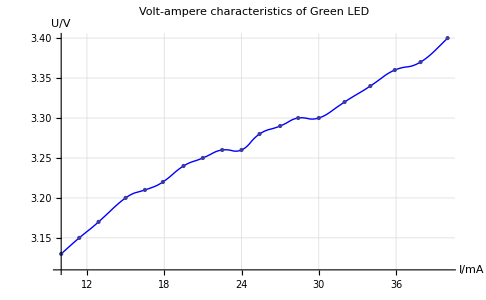

```mathematica
Show[gra1=ListLinePlot[data1,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"I/mA","U/V"},PlotLabel->"Volt-ampere characteristics of Green LED",GridLines->Automatic],ListPlot[data1]]
```

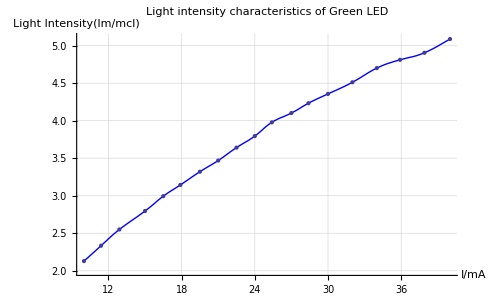

```mathematica
Show[gra2=ListLinePlot[data2,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"I/mA","Light Intensity(lm/mcl)"},PlotLabel->"Light intensity characteristics of Green LED",GridLines->Automatic],ListPlot[data2],PlotRange->{2,5.1}]
```